```mathematica
A={{2,1,1,1},{4,2,1,-1},{201,102,-99,98},{1,2,1,-2}}
```

{{2,1,1,1},{4,2,1,-1},{201,102,-99,98},{1,2,1,-2}}

```mathematica
Det[A]
```

-1800

```mathematica
D1=x1-m
```

{{-1+x1,-3+x1,-1+x1,x1},{-2+x1,-6+x1,-3+x1,2+x1},{2+x1,6+x1,x1,4+x1}}

```mathematica
C2={{x1-m,x2},{x1,x2-m}}
```

{{{{-1+x1,-3+x1,-1+x1,x1},{-2+x1,-6+x1,-3+x1,2+x1},{2+x1,6+x1,x1,4+x1}},x2},{x1,{{-1+x2,-3+x2,-1+x2,x2},{-2+x2,-6+x2,-3+x2,2+x2},{2+x2,6+x2,x2,4+x2}}}}

```mathematica
MatrixForm[D1]
```

(-1+x1 | -3+x1 | -1+x1 | x1
-2+x1 | -6+x1 | -3+x1 | 2+x1
2+x1 | 6+x1 | x1 | 4+x1)

```mathematica
MatrixForm[C2]
```

({{-1+x1,-3+x1,-1+x1,x1},{-2+x1,-6+x1,-3+x1,2+x1},{2+x1,6+x1,x1,4+x1}} | x2
x1 | {{-1+x2,-3+x2,-1+x2,x2},{-2+x2,-6+x2,-3+x2,2+x2},{2+x2,6+x2,x2,4+x2}})

```mathematica
MatrixForm[m]
```

(1 | 3 | 1 | 0
2 | 6 | 3 | -2
-2 | -6 | 0 | -4)

```mathematica
A={{1,3,2},{0,-1,-3}}
```

{{1,3,2},{0,-1,-3}}

```mathematica
B={{1,-1},{0,1},{-2,0}}
```

{{1,-1},{0,1},{-2,0}}

```mathematica
C1=A.B
```

{{-3,2},{6,-1}}

```mathematica
MatrixForm[C1]
```

(-3 | 2
6 | -1)

```mathematica
A={{1,-2,1,0,-4},
     {2,4,6,2,5},
     {-1,2,9,4,7},
     {3,2,7,2,1}};
```

```mathematica
MatrixForm[A]
```

(1 | -2 | 1 | 0 | -4
2 | 4 | 6 | 2 | 5
-1 | 2 | 9 | 4 | 7
3 | 2 | 7 | 2 | 1)

```mathematica
NullSpace[A] // MatrixForm
```

(54 | -59 | -12 | 0 | 40
6 | -1 | -8 | 20 | 0)

```mathematica
x = {{1,2,3},{3,6,8}}
```

{{1,2,3},{3,6,8}}

```mathematica
NullSpace[x]
```

{{-3,0,1},{-2,1,0}}

```mathematica
Inverse[x]
```

Inverse::matsq: Argument {{1, 2, 3}, {3, 6, 8}} at position 1 is not a non-empty square matrix.

Inverse[{{1,2,3},{3,6,8}}]

```mathematica
m={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
Inverse[m] // MatrixForm
```

(d/(-b c+a d) | -b/(-b c+a d)
-c/(-b c+a d) | a/(-b c+a d))

```mathematica
m={{1,3},{2,7}}
```

{{1,3},{2,7}}

```mathematica
Inverse[m]
```

{{7,-3},{-2,1}}

```mathematica
Det[m]
```

1

```mathematica
n={{1,2},{2,4}}
```

{{1,2},{2,4}}

```mathematica
Det[n]
```

0

```mathematica
Inverse[n]
```

Inverse::sing: Matrix {{1, 2}, {2, 4}} is singular.

Inverse[{{1,2},{2,4}}]

```mathematica
Solve[x/2295=2560/1440,x]
```

Set::write: Tag Times in {{1, 2, 3}, {3, 6, 8}}/2295 is Protected.

Solve::ivar: {1, 2, 3} is not a valid variable.

Solve[16/9,{{1,2,3},{3,6,8}}]

```mathematica
Solve[x^3+3x==0,x]
```

Solve::ivar: {1, 2, 3} is not a valid variable.

Solve[{{4,14,36},{36,234,536}}==0,{{1,2,3},{3,6,8}}]

```mathematica
Solve[x/2295-2560/1440==0,x]
```

Solve::ivar: {1, 2, 3} is not a valid variable.

Solve[{{-4079/2295,-4078/2295,-151/85},{-151/85,-1358/765,-4072/2295}}==0,{{1,2,3},{3,6,8}}]

```mathematica
2560/1440
```

16/9

```mathematica
N[16/9]
```

1.77778

```mathematica
x=2295*1.8
```

4131.

```mathematica
√4==2
```

True

```mathematica
4^(1/2)
```

2

```mathematica
7/2
```

7/2

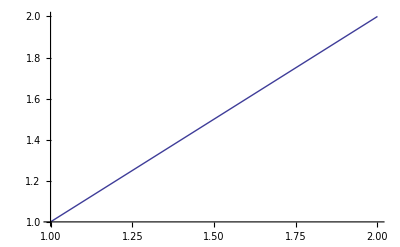

```mathematica
ListLinePlot[{{1,1},{2,2}}]
```

```mathematica
a={{1,1},{2,2}}
```

{{1,1},{2,2}}

```mathematica
a // MatrixForm
```

(1 | 1
2 | 2)

```mathematica
b={{2,3},{4,5}}
```

{{2,3},{4,5}}

```mathematica
b // MatrixForm
```

(2 | 3
4 | 5)

```mathematica
a-b
```

{{-1,-2},{-2,-3}}

```mathematica
b-a // MatrixForm
```

(1 | 2
2 | 3)

```mathematica
b[1]
```

{{2,3},{4,5}}[1]

```mathematica
b
```

{{2,3},{4,5}}

```mathematica
{{100,200,100},{200,200,100},{100,300,100},{200,300,100},{100,200,200},{200,200,200},{100,300,200},{200,300,200}}
```

{{100,200,100},{200,200,100},{100,300,100},{200,300,100},{100,200,200},{200,200,200},{100,300,200},{200,300,200}}

```mathematica
cube={{100,200,100},{200,200,100},{100,300,100},{200,300,100},{100,200,200},{200,200,200},{100,300,200},{200,300,200}}
```

{{100,200,100},{200,200,100},{100,300,100},{200,300,100},{100,200,200},{200,200,200},{100,300,200},{200,300,200}}

```mathematica
cube // MatrixForm
```

(100 | 200 | 100
200 | 200 | 100
100 | 300 | 100
200 | 300 | 100
100 | 200 | 200
200 | 200 | 200
100 | 300 | 200
200 | 300 | 200)

```mathematica
ListPointPlot3D[cube, AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
Show[%29,Background->None]
```

-Graphics3D-

```mathematica
pp={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,1/d,0}}
```

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,1/d,0}}

```mathematica
pp // MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 1/d | 0)

```mathematica
pp'=Transpose[pp]
```

{{-1,0,0,0},{0,1,0,0},{0,0,1,1/d},{0,0,0,0}}

```mathematica
pp'//MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 1/d
0 | 0 | 0 | 0)

```mathematica
param1 = {{1,1,1,1}}
```

{{1,1,1,1}}

```mathematica
pp*param1 // MatrixForm
```

Thread::tdlen: Objects of unequal length in {{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 1/d, 0}}\ {{1, 1, 1, 1}} cannot be combined.

{{1,1,1,1}} {{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,1/d,0}}

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,1/d,0}}

```mathematica
pp*Transpose[param1]//MatrixForm
```

Transpose::nmtx: The first two levels of the one-dimensional list {1, 1, 1, 1} cannot be transposed.

(-Transpose[{1,1,1,1}] | 0 | 0 | 0
0 | Transpose[{1,1,1,1}] | 0 | 0
0 | 0 | Transpose[{1,1,1,1}] | 0
0 | 0 | Transpose[{1,1,1,1}]/d | 0)

```mathematica
param1' = Transpose[param1]
```

Transpose::nmtx: The first two levels of the one-dimensional list {1, 1, 1, 1} cannot be transposed.

Transpose[{1,1,1,1}]

```mathematica
ListLinePlot[p2]
```

ListLinePlot::lpn: p2 is not a list of numbers or pairs of numbers.

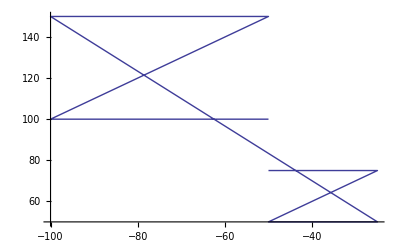

```mathematica
ListLinePlot[p2]
```

```mathematica
p2={{-50,100},{-100,100},{-50,150},{-100,150},{-25,50},{-50,50},{-25,75},{-50,75}}
```

{{-50,100},{-100,100},{-50,150},{-100,150},{-25,50},{-50,50},{-25,75},{-50,75}}

```mathematica
Plot[p2]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[p2]

```mathematica
Plot[p2]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[p2]

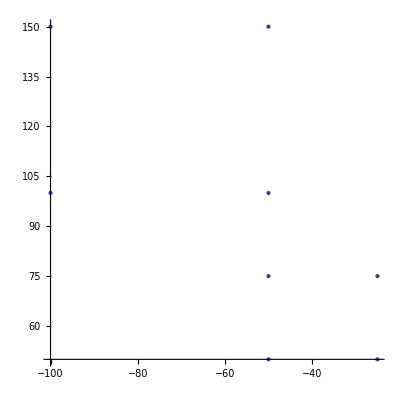

```mathematica
ListPlot[p2,AspectRatio->1]
```

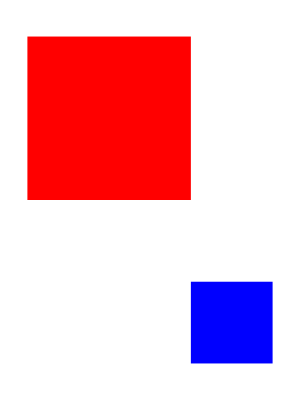

```mathematica
Graphics[{Blue,Rectangle[{-50,50},{-25,75}],Red,Rectangle[{-100,100},{-50,150}]}]
```